```mathematica
(*1 uloha*)
```

```mathematica
r = 0.04; (*urok*)
H0= 100000; (*vklad*)
f[doba_,t_] = H0*(Power[(1+r/doba), t*doba])
```

100000 (1+0.04/doba)^(doba t)

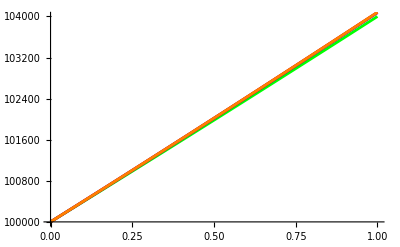

```mathematica
(*ročne*)
n1 = 1;
p1 = Plot[f[1,x], {x, 0, n1}, PlotStyle->Green];
(*mesačne*)
n2= 12.08*n1;
p2 = Plot[f[12, x],{x, 0, n1}, PlotStyle -> Blue];
(*denne*)
n3= 365* n1;
p3= Plot[f[365, x], {x, 0, n1}, PlotStyle->Red];
(*spojité*)
p4 = Plot[H0*Power[E, r*x], {x, 0, n1}, PlotStyle->Orange];
Show[p1, p2, p3,p4]
```

```mathematica
(*2 uloha*)
```

```mathematica
X = 100000;
Y = 1000;
R = 0.04;
n = 10;
sn = X*Power[(1+r), n]; 
v = 1/(1+r);
an = Power[1+r, -n];
```

-Graphics-